# The Quantum Orbits Dynamic Dashboard

## Introduction

```mathematica
dashboardPlotter[{0.05,0.055},1.007,{"tκ","t0","t0"+(2π)/0.055+5ⅈ,"t0"+1.3(2π)/0.055}, {0.05,0.4}]
```

This is a basic example of the Quantum Orbits Dynamic Dashboard (or just Dashboard from here on out).

See below for an documentation of what everything is, and how to use it, as well as some examples of the physics it helps uncover.

#### The multiple elements of the Dashboard are:

Three graphs which show the complex trajectory r_cl(t)=∫_t_s^t (p+A(τ))dτ in the complex x, z and r^2 planes (top left, top centre and bottom centre, respectively).

On bottom right, the time contour in the complex time plane is the blue line.

On bottom left, the relative probability of ionization as a function of momentum, with the current value of momentum as a selector (). This shows exclusively the tunnelling probability, e^(-2Im(∫_t_0^t_s I_p+1/2(p+A(τ))^2 dτ)), normalized to 1 at the maximum of the distribution, which is at p=0.

On top right, the integrand for the Coulomb correction as a function of normalized path length, in its real, imaginary and absolute parts.

#### Some more details and extra information:

There’s tooltips all over the place (or there should be, but they’ve playing up in MM10), so hover your mouse over stuff to try and find out what it is. Try, for example,

dots in the trajectories and the time contour

gray regions

the green and red lines on top and bottom right

the curves on bottom centre

the contours on bottom left show the value of probability

The gray regions on bottom centre and right represent regions where r^2 and (r_cl(t))^2, resp., have a negative real part. This is not catastrophic but these regions should be avoided; for example, molecular correlation potentials must not be trusted there.

The red lines on top and bottom right are the lines where r^2 and (r_cl(t))^2, resp., become real and negative; here √(r^2) has a branch cut.

The green lines, on the other hand, are the positive real axis of r^2 and (r_cl(t))^2, where everything is fine.

Dots on the top and on bottom right indicate the origin of each plot, the start and end of the contour, and a controllable point along it. The start of the contour is usually t_κ=t_s-ⅈ/κ^2, which can be identified as the tunnel entrance.

The colour scale on bottom left is linear but the contours are logarithmic. Thus there is a drop of one order of magnitude between successive thick lines and a drop of 10^(1/10)between successive thin lines (which also mark colour changes).

This contour plot is normalized to the probability at the peak of the field, to zero total momentum.

The contour on bottom right is parametrized uniformly between the different dots. This causes the rate of change dt/ds to change from one segment to the next, which is what causes the abrupt shifts in the graph on top right.

The integral with respect to s of the real and imaginary parts on bottom centre gives the invariant ∫_contour 1/(√((r_cl(t))^2))dt, which is the desired Coulomb correction up to constants.

#### How to control the Dashboard

Most importantly, the time contour itself is editable, by dragging the selectors marked on the kinks of the contour, or by clicking near them (the nearest selector moves).

The momentum can also be changed by dragging the selector marked  on the contour plot on bottom left, or by clicking anywhere on that plot.

For finer control, the text fields below the momentum plot can be used to input specific values for each component. This can also be used to enter values outside those shown on the plot.

The sign of both components can be changed by clicking the + button, which will turn it to a - and then back.

The slider marked Contour progress on the top moves a black dot along the contour the time plane, and along the corresponding space plots.

The r^2 and time plots, on bottom centre and bottom right, have adjustable plot ranges below them. Click Reset to set them to the default setting.

The ionization time t_s, at which the trajectory r_cl(t)=∫_t_s^t (p+A(τ))dτ starts, can be controlled using the input box at top centre. Clicking the "t_s" button sets it to the saddle point time (which obeys 1/2(p+A(t_s))^2+I_p=0), and the "t_0" button sets it to the real part of that. This is useful for investigating the process of deforming the ionization-time integration contour up to the saddle-point time.

The sliders and controls on top right add and control an initial position to the classical position, r_cl(t)=r_init+∫_t_s^t (p+A(τ))dτ. This is required if the start time is set to zero, as the trajectory is meant to start on the ARM boundary.

#### How to call the function

To make new Dashboards, you can use the dashboardPlotter function, though this requires full-blown Mathematica and cannot be done on the CDF player. To see the calling syntax, use

```mathematica
?dashboardPlotter
```

dynamicDashboardPlotter[{F, ω}, κ] plots a dashboard for field amplitude F at frequency ω, for ionization potential κ^2/2.
  
dynamicDashboardPlotter[{F, ω}, κ, path] institutes the desired path, where the strings "tκ", "ts", "t0" and "τ" will be replaced by the corresponding functions of momentum, and "T" is a laser period. Default is {"tκ", "t0", "T"}.
  
dynamicDashboardPlotter[{F, ω}, κ, path, {poinit, ppinit}] specifies initial values of poinit and pp init for p_⊥ and p_∥.

Entering Ctrl+k will pull up templates for convenience (possibly not in V8, though, or it may need Ctrl+Alt+k or something).

### Some physics examples

#### The ‘standard’ contour can fail

because branch cuts of √((r_cl(t))^2) can cross the real axis. Unfortunately, this specific case occurs out in the wings of the distribution where nothing gets observed to begin with. (In essence, the transverse momentum for this case is implausibly large. This causes the transverse coordinate to become very imaginary, and the longitudinal coordinate cannot offset the large and negative (x_cl(t))^2, so the sum becomes negative.)

```mathematica
dashboardPlotter[{0.05,0.055},1.007,{"tκ","tκ"-10ⅈ,"tκ"-10ⅈ+4,"t0"+4,"t0"+15}, {0.7,0.3}]
```

There are two important drawbacks with this scenario, that I can see:
 • It only happens at very low probability. The starting point for this is for transverse momentum just above p_⊥=0.5 for ‘standard’ conditions, and zero longitudinal momentum. This means that the ionization probability there is low (less than 1%), and who knows whether other effects come in to cloud this picture or not. Higher p_⊥ make the behaviour a lot clearer but this really drives the amplitude down.
 • There is still a horizontal bit of the contour before the drop, and this still accumulates phase as any energy the electron has is being integrated along a real time direction. This may or may not mean that the time delay is not actually measurable, but it merits careful consideration.

#### Recolliding electrons

... look quite interesting with these tools.

Consider a ‘standard’ recolliding electron (zero transverse momentum and small, reasonable and positive momentum along the laser polarization) and take the time contour through slightly more than one period. During the recollision, it crosses the branch cut twice!

```mathematica
dashboardPlotter[{0.05,0.055},1.007,{"tκ","tκ"+1.(2π)/0.055,"t0"+1.3(2π)/0.055}, {0.005,0.1}]
```

There are two aspects of this behaviour which look very robust to me.
 • This is very close to the peak of the ionization probability, with probability as high as 98%. This cannot be ignored.
 • After about p_∥=0.075, the branch cuts cross completely the real time axis. It is not clear to me, at all, that there is any way to avoid them.

During the recollision, most of the action is in the plot of (r_cl(t))^2, on bottom centre. It seems the trajectory must loop twice around the origin of that plot, hence the two branch cut crossings. This can be seen by playing with the contour progress slider, or by adding an intermediate point to the contour path at "tκ"+(2π)/0.055.

#### More recollisions

Finally, branch cut crossings and loops around the zero of (r_cl(t))^2 seem even more unavoidable if one takes the end of the contour a few periods further down. (Note, also, that in principle this contour should end after the pulse is finished, so this dragging-out is necessary.)

```mathematica
dashboardPlotter[{0.05,0.055},1.007,{"tκ","t0"+3(2π)/0.055}, {0,0.1}]
```

Points of note:
 • It’s no longer clear to me whether the branch cuts come in pairs or not. It would be nice if they did, as crossing square-root branch cuts twice returns you to the same branch of the Riemann surface, if that even makes sense in the current context, but I don’t know yet whether it’s the case or not.
 • All of the branch cuts definitely do cut the real axis and at this point it’s anyone’s guess what to do with the time integration over the contour.
 • I really, really enjoy the multiple loops around the zero of (r_cl(t))^2 .

#### What I’m working on now

is a way to automatically choose contours that will avoid the branch cuts in situations like this,

```mathematica
dashboardPlotter[{0.05,0.055},1.007,{"tκ","t0","T"}, {0.02,0.9}]
```

or like this

```mathematica
dashboardPlotter[{0.05,0.055},1.007,{"tκ","t0",1.5"T"}, {0.001,0.072}]
```

Notice that these problem points have much higher ionization probabilities!

## Implementation

#### Initialization

```mathematica
Needs["EPToolbox`"]
NotebookEvaluate[
"/home/episanty/Work/CQD/Project/Scratch/functions 28.05 functions file v1.0.6.nb",
EvaluationElements->"InitializationCell"
];
```

```mathematica
$HistoryLength=5;
```

### Dashboard components

#### timeContours

```mathematica
Options[timeContours]={ImageSize->{360,360}};
timeContours[r2function_,rules_,tss_,path_,tRangeNumeric_,OptionsPattern[]]:=Show[{
RegionPlot[
Tooltip[Re[r2function[ret+ⅈ imt]]<0,DisplayForm[Row[{"Re(",Superscript["r_cl(t)","2"],")<0"}]]]
,{ret,tRangeNumeric⟦1,1⟧,tRangeNumeric⟦1,2⟧},{imt,tRangeNumeric⟦2,1⟧,tRangeNumeric⟦2,2⟧}
,AspectRatio->Automatic,AxesOrigin->{0,0},PlotRangePadding->0
,FrameLabel->{"Re(t)","Im(t)"}
,PlotLabel->"time contour"
,PlotStyle->GrayLevel[0.8]
,ImageSize->OptionValue[ImageSize]
],
Sequence@@Table[
ContourPlot[
Im[r2function[ret+ⅈ imt]]==0
,{ret,tRangeNumeric⟦1,1⟧,tRangeNumeric⟦1,2⟧},{imt,tRangeNumeric⟦2,1⟧,tRangeNumeric⟦2,2⟧}
,AspectRatio->Automatic,AxesOrigin->{0,0},PlotRangePadding->0
,ContourStyle->{Thick,selector/.{Less->Red,Greater->RGBColor[0,0.6,0]}}
,ContourLabels->{None,Tooltip[Null,
selector/.{Less->DisplayForm[Row[{"Branch cut.\nIm(",Superscript["r_cl(t)","2"],")=0,\nRe(",Superscript["r_cl(t)","2"],")<0"}]],Greater->DisplayForm[Row[{"Im(",Superscript["r_cl(t)","2"],")=0,\nRe(",Superscript["r_cl(t)","2"],")>0"}]]}
]&}
,RegionFunction->Function[{ret,imt},selector[Re[r2function[ret+ⅈ imt]],0]]
]
,{selector,{Greater,Less}}
]
}]
```

#### timePathPlotter

```mathematica
Options[timePathPlotter]={ImageSize->{360,360}};
timePathPlotter[rules_,t_,sman_,OptionsPattern[]]:=Show[Join[{
ParametricPlot[
{Re[t[s]],Im[t[s]]}
,{s,0,1}
,Frame->True,Axes->False,AxesOrigin->{0,0}
,PlotRangePadding->2
]
,Graphics[{PointSize[Large],Purple,Tooltip[Point[{Re[#],Im[#]}&@Evaluate["ts"/.rules]],"t_s"]}]
,Graphics[{PointSize[Large],Gray,Tooltip[Point[{Re[#],Im[#]}&@Evaluate["tκ"/.rules]],"t_κ"]}]
,Graphics[{PointSize[Large],Green,Tooltip[Point[{Re[t[0]],Im[t[0]]}(*/.s->0*)],"Contour start"]}]
,Graphics[{PointSize[Large],Red,Tooltip[Point[{Re[t[1]],Im[t[1]]}(*/.s->1*)],"Contour end"]}]
,Graphics[{PointSize[Large],Blue,Tooltip[Point[{0,0}],"Time origin"]}]
,Graphics[{PointSize[Large],Black,Tooltip[Point[{Re[t[sman]],Im[t[sman]]}],"t(s)"]}]
},
Graphics[{PointSize[Large],GrayLevel[0.7],Tooltip[Point[{Re[#],Im[#]}],"t_CA"]}]&/@("tCAset"/.rules)
]]
```

#### trajectoryPlotter

```mathematica
Options[trajectoryPlotter]={"PlotRange"->All};
trajectoryPlotter[trajectoryFunction_,label_,sman_,OptionsPattern[]]:=
Show[#,PlotRange->OptionValue["PlotRange"],PlotRangePadding->0.05Max[(#⟦2⟧-#⟦1⟧&)/@(PlotRange/. AbsoluteOptions[#,PlotRange])]]&@(*For better padding, as per mm.se:42495.*)
Show[{
ParametricPlot[
{Re[trajectoryFunction[s]],Im[trajectoryFunction[s]]},{s,0,1}
,AspectRatio->Automatic
,PlotRange->Full
,Frame->True
,Axes->False
,AxesOrigin->{0,0}
,FrameLabel->{"Re("<>label<>")","Im("<>label<>")"}
,PlotLabel->label
,Evaluate@If[label=="r_cl(t)^2",Prolog->{
GrayLevel[0.8],Tooltip[Rectangle[{-1000,-1000},{0,1000}],DisplayForm[Row[{"Re(",Superscript["r_cl(t)","2"],")<0"}]]],
Red,Thick,Tooltip[Line[{{-1000,0},{0,0}}],DisplayForm[Row[{"Branch cut\n",Superscript["r_cl(t)","2"],")<0"}]]]
},##&[]
]
,ImageSize->{360,360}
]
,Graphics[{PointSize[Large],Green,Tooltip[Point[{Re[trajectoryFunction[0]],Im[trajectoryFunction[0]]}],"Contour start"]}]
,Graphics[{PointSize[Large],Red,Tooltip[Point[{Re[trajectoryFunction[1]],Im[trajectoryFunction[1]]}],"Contour end"]}]
,Graphics[{PointSize[Large],Blue,Tooltip[Point[{0,0}],"Origin"]}]
,Graphics[{PointSize[Large],Black,Tooltip[Point[{Re[trajectoryFunction[sman]],Im[trajectoryFunction[sman]]}],label]}]
}]
```

#### timeIntegrandPlotter

```mathematica
Options[timeIntegrandPlotter]={ImageSize->{360,360}};
timeIntegrandPlotter[rer2function_,t_,OptionsPattern[]]:=ParametricPlot[{
Tooltip[{s,Re[-(rer2function[s])^(-1/2)D[t[ss],ss]/.{ss->s}]},"Re"],
Tooltip[{s,Im[-(rer2function[s])^(-1/2)D[t[ss],ss]/.{ss->s}]},"Im"],
Tooltip[{s,Abs[-(rer2function[s])^(-1/2)D[t[ss],ss]/.{ss->s}]},"Abs"]
},{s,0,1}
,PlotRange->{{0,1},Full}
,AspectRatio->1/3
(*,PlotPoints->20*)
,Frame->True
,AxesStyle->Gray
,FrameLabel->{Style[ToString[s,TraditionalForm],Larger],""}
,PlotLabel->"Re, Im and Abs of -1/(√r_cl)dt/ds over the contour"
,ImageSize->OptionValue[ImageSize]
]
```

### Ionization probability

#### ionizationProbabilityColorFunction

```mathematica
ionizationProbabilityColorFunction=(Blend[{RGBColor[0.4,0,0],Red,Orange,Yellow},#]&);
```

#### colourScale and colorfunction

```mathematica
colourScale[{pomax_,ppmax_},{F_,ω_},κ_]:=colourScale[{pomax,0,ppmax},{F,ω},κ]=ContourPlot[
y,
{x,0,0.075},{y,0,1}
,AspectRatio->Automatic
,Contours->10^Range[Floor[Log[10,ⅇ^(2volkovExponent[{pomax,0,ppmax},{F,ω,κ}])/ⅇ^(2volkovExponent[{0,0,0},{F,ω,κ}])]],-0,0.1]
,PlotRangePadding->None
,FrameTicks->{{None,{10^Range[-1,0,0.1],ToString[#,TraditionalForm]&/@Evaluate[10^(ToString/@Range[-1,0,0.1])/.{10^("0.")->1}]}ᵀ},{None,None}}
,ContourLabels->None
,ColorFunction->ionizationProbabilityColorFunction
,ImageSize->{70,200}
]
```

```mathematica
colourScale[{1,1.5},{0.05,0.055},1.007]
```

-Graphics-

#### ionizationProbabilityPlot

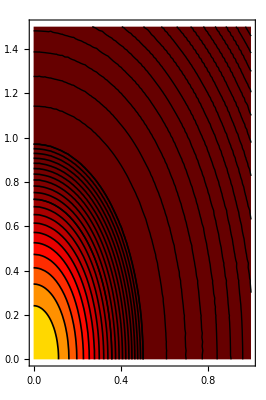

```mathematica
ClearAll[ionizationProbabilityPlot]
ionizationProbabilityPlot[{F_,ω_,κ_}]:=ionizationProbabilityPlot[{F,ω,κ},a]=Module[
{ppmax=1.5,pomax=1},
Show[
cleanContourPlot[ContourPlot[
ⅇ^(2volkovExponent[{ppo,0,ppp},{F,ω,κ}])/ⅇ^(2volkovExponent[{0,0,0},{F,ω,κ}])
,{ppo,0,pomax},{ppp,0,ppmax}
,PlotRange->Full
,Contours->10^Range[-2,0,0.1]
,ColorFunction->ionizationProbabilityColorFunction
,ContourStyle->None
,PlotPoints->20
,AspectRatio->Automatic
,PlotRangePadding->None
,ImageSize->{{360},{340}}
]],
ContourPlot[
ⅇ^(2volkovExponent[{ppo,0,ppp},{F,ω,κ}])/ⅇ^(2volkovExponent[{0,0,0},{F,ω,κ}])
,{ppo,0,pomax},{ppp,0,ppmax}
,PlotRange->Full
,Contours->10^Range[-2,0,0.1]
,ContourShading->None
,ContourStyle->{{Thickness[0.003],Black}}
,PlotPoints->20
],
(ContourPlot[
ⅇ^(2volkovExponent[{ppo,0,ppp},{F,ω,κ}])/ⅇ^(2volkovExponent[{0,0,0},{F,ω,κ}])
,{ppo,0,pomax},{ppp,0,ppmax}
,PlotRange->Full
,Contours->10^Range[Floor[Log[10,ⅇ^(2volkovExponent[{pomax,0,ppmax},{F,ω,κ}])/ⅇ^(2volkovExponent[{0,0,0},{F,ω,κ}])]],-0,1]
,ContourShading->None
,ContourStyle->{Black}
,PlotPoints->20
]/.{
Tooltip[expr_,tooltip_]:>Tooltip[expr,DisplayForm[SuperscriptBox[10,Log[10,tooltip]]]]
})
]
]
ionizationProbabilityPlot[stdpars]
```

### Control elements

#### rangeReset

```mathematica
(*ClearAll[rangeReset];*)
SetAttributes[rangeReset,HoldFirst]
rangeReset[range_,{label1_,label2_}]:=Row[{
Grid[{
{InputField[Dynamic[range⟦1,1⟧],FieldSize->3],"≤"<>label1<>"≤",InputField[Dynamic[range⟦1,2⟧],FieldSize->3]},
{InputField[Dynamic[range⟦2,1⟧],FieldSize->3],"≤"<>label2<>"≤",InputField[Dynamic[range⟦2,2⟧],FieldSize->3]}
}],
"  ",
Button["Reset",range={{All,All},{All,All}},ImageSize->Medium]
}]
```

#### momentumPlaneControls

```mathematica
SetAttributes[momentumPlaneControls,HoldAll];
momentumPlaneControls[{po_,py_,pp_},{F_,ω_,κ_}]:=Grid[{
{Dynamic[Text[
"Probability = "<>(If[#≤10^-2,
ToString[ScientificForm[#,2],TraditionalForm],
ToString[NumberForm[#,2]]
]&[ⅇ^(2volkovExponent[{po,py,pp},{F,ω,κ}])/ⅇ^(2volkovExponent[{0,0,0},{F,ω,κ}])])
]]},
{
LocatorPane[
Dynamic[
{Abs[po],Abs[pp]},
((po=If[po≠0,Sign[po]#⟦1⟧,#⟦1⟧]);(pp=If[pp≠0,Sign[pp]#⟦2⟧,#⟦2⟧]);updateDefinitions[])&
],
ionizationProbabilityPlot[{F,ω,κ}]
],
colourScale[{1,0,1.5},{F,ω},κ]
}
,{Row[{Text["p_⊥="],Button[Dynamic[po/.{a_/;(a≥0)->"+",a_/;(a<0)->"-"}],po=-po],InputField[Dynamic[Abs[po],(po=If[po≠0,Sign[po]#,#])&],FieldSize->3],Text[" p_∥="],Button[Dynamic[pp/.{a_/;(a≥0)->"+",a_/;(a<0)->"-"}],pp=-pp],InputField[Dynamic[Abs[pp],(pp=If[pp≠0,Sign[pp]#,#])&],FieldSize->3]}]
}}]
```

#### contourProgressController

```mathematica
SetAttributes[contourProgressController,HoldAll];
contourProgressController[sMan_]:=Row[{Text["Contour progress: "],Manipulator[Dynamic[sMan],Appearance->{"Labeled"}]}]
```

#### tsController

```mathematica
SetAttributes[tsController,HoldAll];
tsController[Δtss_,baretss_,tss_,{F_,ω_,κ_}]:=Row[{Text["t_s="],
InputField[
Dynamic[tss,Function[input,(Δtss=Evaluate[input/.{"tκ"->baretss-ⅈ/κ^2,"ts"->baretss,"t0"->Re[baretss],"τ"->Im[baretss],"T"->2π/ω}]-baretss),HoldRest]],
FieldSize->12]
,Button["t_s",Δtss=0],Button["t_0",Δtss=-ⅈ Im[baretss]]
}]
```

#### rInitController

```mathematica
SetAttributes[rInitController,HoldAll];
rInitController[xinit_,zinit_,rInitRange_]:=Grid[{
{Text["x_init "],Button[Dynamic[xinit/.{a_/;(a≥0)->"+",a_/;(a<0)->"-"}],xinit=-xinit],
Manipulator[Dynamic[Abs[xinit],(xinit=If[xinit≠0,Sign[xinit]#,#])&],{0,rInitRange},Appearance->{"Labeled"}]},
{Text["z_init "],Button[Dynamic[zinit/.{a_/;(a≥0)->"+",a_/;(a<0)->"-"}],zinit=-zinit],
Manipulator[Dynamic[Abs[zinit],(zinit=If[zinit≠0,Sign[zinit]#,#])&],{0,rInitRange},Appearance->{"Labeled"}]}
}]
```

### dashboardPlotter

```mathematica
dashboardPlotter[{F_,ω_},κ_,initialpath_: {"tκ","t0","T"},{poinit_:0.15,ppinit_:0.15}]:=DynamicModule[
{po=poinit,pp=ppinit,py=0,sMan=0.1,t,rules
,trajectory
,expr,labels
,path,barepath=initialpath,Δpath=Table[0,{Length[initialpath]}]
,tss,baretss,Δtss=0
,tCAset,showtCAs=True
,xinit=0,zinit=0,rInitRange=0.15
,r2range={{All,All},{All,All}},r2FullRange=All,r2plot
,tRangeSymbolic={{All,All},{All,All}},tRangeNumeric
,updateDefinitions
,scale=1
},
updateDefinitions[]:=(
baretss=ts[{po,py,pp},{F,ω,κ}];
tss=baretss+Δtss;
rules:={"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"-> 2π/ω,"tCAset"->tCAset};
tRangeNumeric=(({{
If[#⟦1,1⟧===All,"t0"-10,#⟦1,1⟧],If[#⟦1,2⟧===All,Re[Last[path]]+10,#⟦1,2⟧]
},{
If[#⟦2,1⟧===All,-10,#⟦2,1⟧],If[#⟦2,2⟧===All,Max[Im[tss]+10,15],#⟦2,2⟧]
}}&[tRangeSymbolic])/.rules);
tCAset=If[TrueQ[showtCAs],(tCA/.allQuantumClosestApproachTimes[{po,0,pp},{F,ω,κ},{xinit,0,zinit},"Range"->Complex@@@Transpose[tRangeNumeric]]),{}];
path=Evaluate[barepath/.rules]+Δpath;
t=Interpolation[Evaluate[{Range[0,1,1/(Length[path]-1)],path}ᵀ],InterpolationOrder->1];
trajectory:=Function[t,complexTrajectory[t,{po,py,pp}, {F,ω,κ},rInit->{xinit,0,zinit},forcets->tss]];
);
Dynamic[updateDefinitions[];""]

Framed[Grid[
{{(*Top row: controllers.*)
contourProgressController[sMan],
tsController[Δtss,baretss,tss,{F,ω,κ}],
rInitController[xinit,zinit,rInitRange]
},{(*Middle row*)
Dynamic[trajectoryPlotter[trajectory[t[#]]⟦1⟧&,"x_cl(t)",sMan,"PlotRange"->All]],
Dynamic[trajectoryPlotter[trajectory[t[#]]⟦3⟧&,"z_cl(t)",sMan,"PlotRange"->All]],
Dynamic[timeIntegrandPlotter[Total[trajectory[t[#]]^2]&,t,ImageSize->{720,360}]]
},{(*Bottom row*)
(*Momentum plane / ionization probability*)
momentumPlaneControls[{po,py,pp},{F,ω,κ}]
,(*r^2 plane - trajectory*)
Column[{
Dynamic[
trajectoryPlotter[Total[trajectory[t[#]]^2]&,"r_cl(t)^2",sMan,"PlotRange"->r2range]
]
,(*r^2 plane range controls*)
rangeReset[r2range,{"Re(r^2)","Im(r^2)"}]
},Center]
,(*time plane - path chooser.*)
Column[{
LocatorPane[
Dynamic[
Join[(*{Re[path],Im[path]}ᵀ*){Re[#],Im[#]}&/@path,{{Re[tss],Im[tss]}}],
Function[points,
(Δpath=(Complex@@@Most[points])-Evaluate[barepath/.rules]);
(Δtss=Complex@@Last[points]-baretss);
updateDefinitions[]
,HoldRest]
],
Dynamic[
Show[
timeContours[Total[trajectory[#]^2]&,rules,tss,path,tRangeNumeric,ImageSize->{720,360}],
timePathPlotter[rules,t,sMan]
]
]
]
,InputField[Dynamic[scale]]
,(*Time plane range controls*)
rangeReset[tRangeSymbolic,{"Re(t)","Im(t)"}]
},Center]
}}
]]
,SaveDefinitions->True]
```

```mathematica
dashboardPlotter[{0.05,0.055},1.007,{"t0","t0"+(2π)/0.055+10ⅈ,"t0"+1.3(2π)/0.055}, {0.05,0.1}]
```

```mathematica
profileDynamics[
dashboardPlotter[{0.05,0.055},1.007,{"t0","t0"+(2π)/0.055+10ⅈ,"t0"+1.3(2π)/0.055}, {0,0.1}]
]
```

```mathematica
(*MM.SE/q/8045*)
ClearAll[profileDynamics];
Options[profileDynamics]={"Print"->False};
profileDynamics[d_,OptionsPattern[]]:=With[
{print=OptionValue["Print"]},
Module[{counter={}},
DynamicModule[
{diag,start,tag},
diag[]:=CreateDocument[Column[{
Button["Reset counter",counter=start],
Dynamic@Grid[Join[
{{"Dynamic expression","Count","Time"}},MapAt[Short,#,1]&/@counter
]]
}]];
CellPrint@ExpressionCell[Button["See profiling information",diag[]]];
d//.{
i:Annotation[_,{tag,___}]:>i,
e:Dynamic[sth:Except[First[{_,tag}]],rest___]:>With[
{pos=1+Length@counter,catalog=Annotation[InputForm@e,{tag,Unique["profileDynamics`annot"]}]},
AppendTo[counter,{catalog,0,0.}];
Dynamic[First@{Refresh[
If[print,Print[catalog]];++counter[[pos,2]];
(counter[[pos,3]]+=First@#;Last@#)&[AbsoluteTiming[Refresh[sth]]],
None],tag},rest]/;True
]
}//(start=counter;#)&
]
]
]
```

```mathematica
testingIonizationPlot[{F_,ω_},κ_,initialpath_: {"tκ","t0","T"},{poinit_:0.15,ppinit_:0.15}]:=DynamicModule[
{po=poinit,pp=ppinit,py=0,sMan=0.1,t,rules,singularpoint,r2,poTrajectory,pyTrajectory,ppTrajectory,re2Trajecotry,expr,labels
,path,barepath=initialpath,Δpath=Table[0,{Length[initialpath]}]
,tss,baretss,Δtss=0
,xinit=0,zinit=0,range=0.15
,r2range={{All,All},{All,All}},r2FullRange=All,r2plot
,trange={{All,All},{All,All}}
},
Dynamic[
(*definitions=(
baretss=ts[pp,κ,ω,F,po,py];
tss=baretss+Δtss;
rules={"tκ"->tss-ⅈ/κ^2,"ts"->tss,"t0"->Re[tss],"τ"->Im[tss],"T"-> 2π/ω};
path=Evaluate[barepath/.rules]+Δpath;
t=Interpolation[Evaluate[{Range[0,1,1/(Length[path]-1)],path}ᵀ],InterpolationOrder->1];
r2=(xinit+po(tt-tss))^2+py^2(tt-tss)^2+(zinit+pp(tt-tss)+F/ω^2(Cos[ω tt]-Cos[ω tss]))^2;
poTrajectory=xinit+po(t[s]-tss);
pyTrajectory=py(t[s]-tss);
ppTrajectory=zinit+pp(t[s]-tss)+F/ω^2(Cos[ω t[s]]-Cos[ω tss]);
re2Trajecotry=r2/.{tt->t[s]};
);*)""
]

Framed[Grid[
{
(*{(*Top row: controllers.*)
Row[{Text["Contour progress: "],Manipulator[Dynamic[sMan],Appearance->{"Labeled"}]}],
Row[{Text["t_s="],
InputField[
Dynamic[tss,Function[input,(Δtss=Evaluate[input/.{"tκ"->baretss-ⅈ/κ^2,"ts"->baretss,"t0"->Re[baretss],"τ"->Im[baretss],"T"->2π/ω}]-baretss),HoldRest]],
FieldSize->12]
,Button["t_s",Δtss=0],Button["t_0",Δtss=-ⅈ Im[baretss]]
}],
Grid[{
{Text["x_init "],Button[Dynamic[xinit/.{a_/;(a≥0)->"+",a_/;(a<0)->"-"}],xinit=-xinit],
Manipulator[Dynamic[Abs[xinit],(xinit=If[xinit≠0,Sign[xinit]#,#])&],{0,range},Appearance->{"Labeled"}]},
{Text["z_init "],Button[Dynamic[zinit/.{a_/;(a≥0)->"+",a_/;(a<0)->"-"}],zinit=-zinit],
Manipulator[Dynamic[Abs[zinit],(zinit=If[zinit≠0,Sign[zinit]#,#])&],{0,range},Appearance->{"Labeled"}]}
}]
}
,
{(*Middle row*)
Dynamic[trajectoryPlotter[poTrajectory,"x_cl(t)",sMan,"PlotRange"->All]],
Dynamic[trajectoryPlotter[ppTrajectory,"z_cl(t)",sMan,"PlotRange"->All]],
Dynamic[timeIntegrandPlotter[re2Trajecotry,t,ImageSize->{720,360}]]
}
,*)
{(*Bottom row*)
(*Momentum plane / ionization probability*)
Grid[{
{Dynamic[Text[
"Probability = "<>(If[#≤10^-2,
ToString[ScientificForm[#,2],TraditionalForm],
ToString[NumberForm[#,2]]
]&[ⅇ^(2exponent[{po,py,pp},{F,ω},κ])/ⅇ^(2exponent[{0,0,0},{F,ω},κ])])
]]},
{
(*Overlay[{
ionizationProbabilityColours[{F,ω},κ],
LocatorPane[
Dynamic[
{Abs[po],Abs[pp]},
((po=If[po≠0,Sign[po]#⟦1⟧,#⟦1⟧]);(pp=If[pp≠0,Sign[pp]#⟦2⟧,#⟦2⟧]);definitions)&
],
(*ionizationProbabilityPlot[stdpars]*)
ionizationProbabilityContours[{F,ω},κ]
]
},All,2,Alignment->Center]*)
LocatorPane[
Dynamic[
{Abs[po],Abs[pp]},
((po=If[po≠0,Sign[po]#⟦1⟧,#⟦1⟧]);(pp=If[pp≠0,Sign[pp]#⟦2⟧,#⟦2⟧]);(*definitions*))&
],
(*Show[Graphics[],PlotRange->{{0,1},{0,1.5}},AspectRatio->Automatic,ImageSize->{{360},{340}},Frame->True]*)
ionizationProbabilityPlot[{F,ω,κ},0]
(*ionizationProbabilityContours[{F,ω},κ]*)
]
,
colourScale[{1,0,1.5},{F,ω},κ]
}
,{Row[{Text["p_⊥="],Button[Dynamic[po/.{a_/;(a≥0)->"+",a_/;(a<0)->"-"}],po=-po],InputField[Dynamic[Abs[po],(po=If[po≠0,Sign[po]#,#])&],FieldSize->3],Text[" p_∥="],Button[Dynamic[pp/.{a_/;(a≥0)->"+",a_/;(a<0)->"-"}],pp=-pp],InputField[Dynamic[Abs[pp],(pp=If[pp≠0,Sign[pp]#,#])&],FieldSize->3]}]
}}]
(*,
(*r^2 plane - trajectory*)
Column[{
Dynamic[
trajectoryPlotter[re2Trajecotry,"r_cl(t)^2",sMan,"PlotRange"->r2range]
]
,(*r^2 plane range controls*)
rangeReset[r2range,{"Re(r^2)","Im(r^2)"}]
},Center]
,
(*time plane - path chooser.*)
Column[{
LocatorPane[
Dynamic[
{Re[path],Im[path]}ᵀ~Join~{{Re[tss],Im[tss]}},
Function[points,(Δpath=(Complex@@@points⟦1;;-2⟧)-Evaluate[barepath/.rules]);(Δtss=Complex@@points⟦-1⟧-baretss),HoldRest]
],
Dynamic[
Show[
timecontours=timeContours[r2,rules,tss,path,trange,ImageSize->{720,360}],
timepath=timePathPlotter[rules,t,sMan]
]
]
],
(*Time plane range controls*)
rangeReset[trange,{"Re(t)","Im(t)"}]
},Center]*)
}
}
]]

,SaveDefinitions->True]
```

```mathematica
profileDynamics@testingIonizationPlot[{0.05,0.055},1.007,{"t0","t0"+(2π)/0.055+10ⅈ,"t0"+1.3(2π)/0.055}, {0,0.1}]
```

```mathematica
Quit[]
```

```mathematica
1+1
```

2

```mathematica
dashboardPlotter::usage="dynamicDashboardPlotter[{F, ω}, κ] plots a dashboard for field amplitude F at frequency ω, for ionization potential \!\(\*SuperscriptBox[\(κ\), \(2\)]\)/2.
  
dynamicDashboardPlotter[{F, ω}, κ, path] institutes the desired path, where the strings \"tκ\", \"ts\", \"t0\" and \"τ\" will be replaced by the corresponding functions of momentum, and \"T\" is a laser period. Default is {\"tκ\", \"t0\", \"T\"}.
  
dynamicDashboardPlotter[{F, ω}, κ, path, {poinit, ppinit}] specifies initial values of poinit and pp init for \!\(\*SubscriptBox[\(p\), \(⊥\)]\) and \!\(\*SubscriptBox[\(p\), \(∥\)]\).";
```

Example usage:

```mathematica
(*dashboardPlotter[{0.05,0.055},1.007,{"t0","t0"+(2π)/0.055+10ⅈ,"t0"+1.3(2π)/0.055}, {0,0.1}]*)
```